```mathematica
This file calculates the reaction rate constants for the 
- MP+RQ<->MPR+Q
- MT+P<->MP+T
- P+RQ->PR+Q
```

The different starting concentrations for [MP] are: {{2.27205,3.6077,5.2083,6.68009},{2.5189,3.94945,5.60712,7.15436},{2.76575,4.29121,6.00593,7.62863},{3.0126,4.63297,6.40474,8.10291},{3.25945,4.97473,6.80356,8.57718},{3.5063,5.31648,7.20237,9.05145},{3.75315,5.65824,7.60119,9.52573},{4.,6.,8.,10.}}

Reporter reaction:

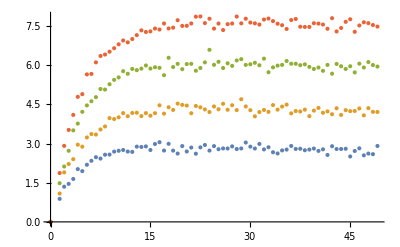

Template Recovery:

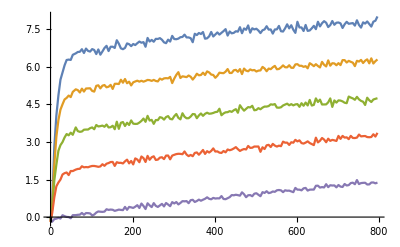

Discard pathway:

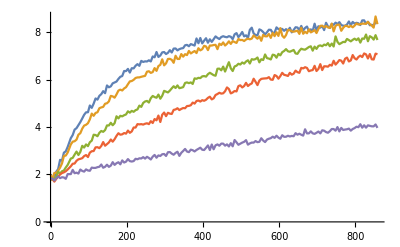

```mathematica
(*Extract the concentration of [BP] and compare it with the actual possible initial [BP] concentration. Create an that takes as extrema the different [BP] concentration. Lower limit is from Cy3 and upper limit is the one that was aimed to be reproduced in the reaction*)
(*Generate 6 sets of initial concentrations*)
(*Also plot the data from reporter characterization, template recovery and discard pathway*)
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Btype="B1b";
Ptype="P28-5";
str=Btype<>Ptype;
Clear[concC];
(*Import the relevant data*)
data=Import["2. Reporters\\Data\\"<>str<>".wl"];
data=data[[2;;5]];
concV=Import["2. Reporters\\Conc\\"<>str<>"BPi.wl"];
concC=Import["2. Reporters\\Conc\\"<>str<>"RQi.wl"];
concBT=Import["3. Template recovery\\Conc\\BT\\"<>Btype<>Ptype<>".wl"];
concBL=Import["4. Discard Pathway\\Conc\\BL\\"<>Btype<>Ptype<>".wl"];
concPRiTR=Import["3. Template recovery\\Conc\\PR\\"<>Btype<>Ptype<>".wl"];
concBPRiDP=Import["4. Discard pathway\\Conc\\BPR\\"<>Btype<>Ptype<>".wl"];
datarange=Import["3. Template recovery\\Data\\"<>str<>".wl"];
datarangeDP=Import["4. Discard pathway\\Data\\"<>str<>".wl"];
cut[x_,t_]:=(For[i=1,i<=Length[x[[1]]],i++,If[x[[1]][[i]][[1]]>t,Break[]];];ret={};
For[j=1,j<=Length[x],j++,AppendTo[ret,x[[j]][[1;;Min[i-1,Length[x[[j]]]-1]]]]];
Return[ret];);
datarangeDP=cut[datarangeDP,1000];
datarange=cut[datarange,1000];
concRQred=Import["3. Template recovery\\Conc\\RQ\\"<>Btype<>Ptype<>".wl"];concRQred2=Import["4. Discard pathway\\Conc\\RQ\\"<>Btype<>Ptype<>".wl"];
concPo=Import["3. Template recovery\\Conc\\P\\"<>Btype<>Ptype<>".wl"];concPo2=Import["4. Discard pathway\\Conc\\P\\"<>Btype<>Ptype<>".wl"];


If[Btype=="B1",col=1];
If[Btype=="B1a",col=2];
If[Btype=="B1b",col=3];
If[Ptype=="P29-5",row=1];
If[Ptype=="P28-5",row=2];
If[Ptype=="P27-5",row=3];
If[Ptype=="P27-4",row=4];
(*RQo=concRQred[[row]][[col]];
RQo2=concRQred2[[col]][[row]];*)
concBP=Import["2. Reporters\\Conc\\"<>str<>"BPi.wl"];
concBPid={0,4,6,8,10};
iter=8;
create[]:=(
arr2={concBP[[2;;5]]};
arr=concBP;
For[i=1,i<=iter-1,i++,
For[j=1,j<=Length[concBP],j++,
arr[[j]]=concBP[[j]]+i*(concBPid[[j]]-concBP[[j]])/(iter-1)];
AppendTo[arr2,arr[[2;;5]]];
];
Return[arr2]
)
(*The array that stores the different [BP] concentrations*)
iter=create[];
Print["The different starting concentrations for [MP] are: ", iter]
clean[x_]:=(y=x;For[i=1,i<=Length[x],i++,y[[i]]=Table[{x[[i]][[j]][[1]],x[[i]][[j]][[2]]-x[[i]][[1]][[2]]},{j,1,Length[x[[i]]]}]];Return[y];)
(*ListPlot[datarangeDP,Joined->True]*)
(*datarangeDP=clean[datarangeDP];*)

Print["Reporter reaction:"]
ListPlot[data]

Print["Template Recovery:"]
ListPlot[datarange,Joined->True]

Print["Discard pathway:"]
ListPlot[datarangeDP,Joined->True]
```

```mathematica
iter
```

{{2.27018,3.59204,5.1932,6.66193},{2.5173,3.93604,5.59417,7.13879},{2.76442,4.28003,5.99514,7.61566},{3.01153,4.62402,6.39611,8.09253},{3.25865,4.96802,6.79709,8.5694},{3.50577,5.31201,7.19806,9.04626},{3.75288,5.65601,7.59903,9.52313},{4.,6.,8.,10.}}

Set of [BP] concentration: {2.27205,3.6077,5.2083,6.68009}

Num evaluations:6962

Forward and backward reaction rates: {0.00799405,0.0001}

Error: 17.7317

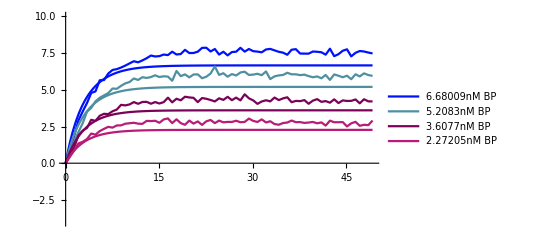

***************************************************************************************

***************************************************************************************

Set of [BP] concentration: {2.5189,3.94945,5.60712,7.15436}

Num evaluations:6962

Forward and backward reaction rates: {0.00683335,0.0001}

Error: 5.93409

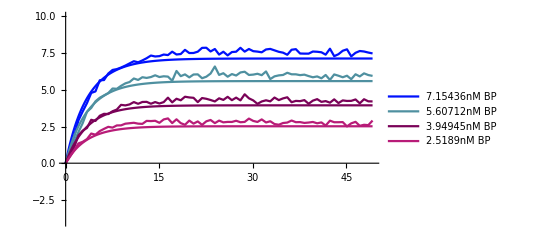

***************************************************************************************

***************************************************************************************

Set of [BP] concentration: {2.68278,4.16247,5.82575,7.39977}

Num evaluations:6962

Forward and backward reaction rates: {0.00607482,0.0001}

Error: 2.56545

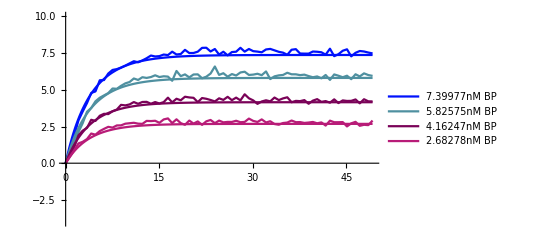

***************************************************************************************

***************************************************************************************

Set of [BP] concentration: {3.0126,4.63297,6.40474,8.10291}

Num evaluations:6962

Forward and backward reaction rates: {0.00519278,0.00189453}

Error: 1.47643

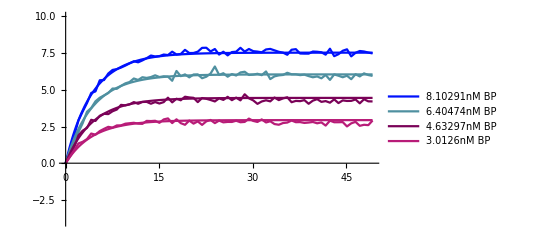

***************************************************************************************

***************************************************************************************

Set of [BP] concentration: {3.25945,4.97473,6.80356,8.57718}

Num evaluations:6962

Forward and backward reaction rates: {0.00480102,0.00369035}

Error: 2.14561

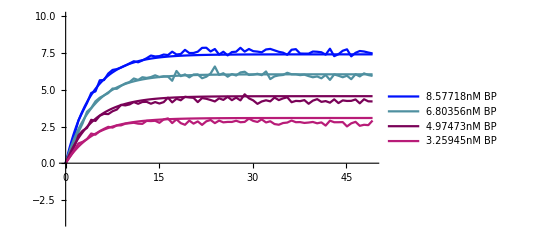

***************************************************************************************

***************************************************************************************

Set of [BP] concentration: {3.5063,5.31648,7.20237,9.05145}

Num evaluations:6962

Forward and backward reaction rates: {0.00443881,0.00525251}

Error: 3.30161

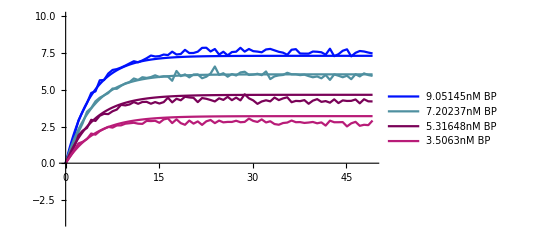

***************************************************************************************

***************************************************************************************

Set of [BP] concentration: {3.75315,5.65824,7.60119,9.52573}

Num evaluations:6962

Forward and backward reaction rates: {0.00410393,0.00639049}

Error: 4.71973

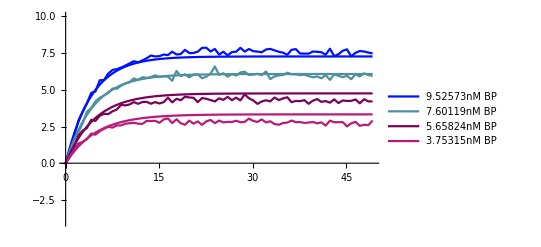

***************************************************************************************

***************************************************************************************

Set of [BP] concentration: {4.,6.,8.,10.}

Num evaluations:6962

Forward and backward reaction rates: {0.00379432,0.00747597}

Error: 6.27521

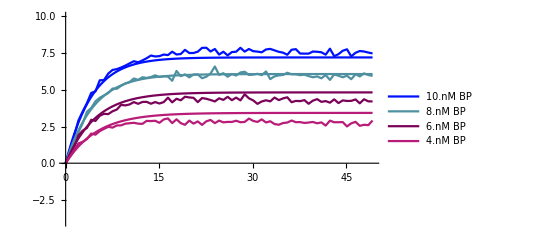

***************************************************************************************

***************************************************************************************

Total time taken (seconds): 363.1770809

```mathematica
(*This pipeline finds the best reaction rate constants for the different initial [BP] concentrations used*)
(*Reaction rate prediction works as what was seen in Lock_opening_final.nb file*)
fig={};
rates={};
t1=AbsoluteTime[];
var=concC;
Tinterest=10;(*For t<Tinterest, weight =1. For t>Tinterest, weight=0.2*)
kstart=0.001;(*Start point of forward reaction*)
kend=.01;(*End point of forward reaction*)
kstart2=.0001;(*Start point of backward reaction*)
kend2=.01;(*End point of forward reaction*)
fact=1.04;(*Factor with which forward reaction rate increases*)
fact2=1.04;(*Factor with which backward reaction rate increases*)

f1[x_]:=var(*RQ initial concentration. Check if this is variable or 40?*);

For[con=1,con<=Length[iter],con++,
concV=iter[[con]];
If[con==3,concV=concV*0.97];
Print["Set of [BP] concentration: ",concV];
concC=Array[f1,4];
Clear[t,k1,k2,k3,k4,k5,k5r,k6,p,p0,p1,y];
reverse=1;(*If 1, use a 2 parameter model, else use 1 parameter model*)
(*functions that return the difference b/w experimental and fitted model. Takes in the parametric solution (y), the conc list (dnew2),; k1, k2 for it; and the index of the dnew2 array, and *)
diff=1;
tabdiff[y_,t_,k1_,k2_]:=(q=t[[1;;,1]];p=Table[{q[[i]],y[k1,k2][q[[i]]]/.sol[[j]]},{i,1,Length[q],diff}];
p0=Table[{q[[i]],t[[i]][[2]]},{i,1,Length[q],diff}];
p1=Table[p[[i]][[2]]-p0[[i]][[2]],{i,1,Length[p],1}];
Return[{p0,p1}];);

ff[x_]:=0;
(*stores the parametric solution of the different differential equations*)
sol=Array[ff,Length[data]];
For[j=1,j≤Length[data],j++,
q=data[[j]][[1;;,1]];
sol[[j]]=ParametricNDSolve[{y'[t]==k1*(concC[[j]]-y[t])*(concV[[j]]-y[t])-k2*y[t]^2,y[0]==0},y,{t,q[[1]],q[[Length[q]]]},{k1,k2}]];

(* BP+RQ<->BPR+Q; y=[BPR]*)
(*Technique#3: Parameter fit that minimizes overall tries to fit for initial times*)
(*Start numerical evaluation of the parameter space*)
reverse=1;
If[reverse==0,kstart2=1;kend2=1];
result=100000;result2={kstart,kstart2};
No=IntegerPart[Log[(kend/kstart)]/Log[fact]]+1;
No2=IntegerPart[Log[(kend2/kstart2)]/Log[fact2]]+1;
Print["Num evaluations:",No*No2];
If[reverse==0,No2=1];
c1=1;
f0[x_,y_]:=0;
error=Array[f0,{No,No2}];
error2={};
For[k10=kstart,k10≤kend,k10=k10*fact,
c10=1;
For[k20=kstart2,k20≤kend2,k20=k20*fact2,
temp0=0;
For[j=1,j≤Length[data],j++,
hello=tabdiff[y,data[[j]],k10,k20];
temparr=hello[[2]];
ttt=hello[[1]];
For[i=1,i<=Length[temparr],i++,
sump=0;
If[ttt[[i]][[1]]<Tinterest,
sump+=1.0(temparr[[i]]*temparr[[i]]);
,
sump+=0.1(temparr[[i]]*temparr[[i]])
];
temp0+=sump;
]];
temp=temp0;
If[c1==1 &&c10==1, result=temp];
error[[c1]][[c10++]]=temp;
error2=AppendTo[error2,{Log[k10],Log[k20],temp}];
(*If new difference between lists is small, remember that parameter set*)
If[temp<result,result=temp;result2={k10,k20}];
]c1++;
];
Print["Forward and backward reaction rates: ",result2];
Print["Error: ",result];
AppendTo[rates,result2];
finplot[k_]:=(
SeedRandom[k+1];
xx=RandomReal[];
yy=RandomReal[];
zz=RandomReal[];
For[j=1,j≤Length[data],j++,
s1=ListPlot[data[[k]],Joined->True,PlotRange->All,PlotStyle->RGBColor[xx,yy,zz]];
s2=Plot[If[reverse==1,y[result2[[1]],result2[[2]]][t]/.sol[[k]],y[result2[[1]]][t]/.sol[[k]]],{t,q[[1]],q[[Length[q]]]},PlotRange->{-4,10},PlotStyle->RGBColor[xx,yy,zz],PlotLegends->{ToString[concV[[k]]]<>"nM BP"}];
s2=Show[s2,s1];
Return[s2]]);

Print[Show[{finplot[4],finplot[3],finplot[2],finplot[1]}]];
Print["***************************************************************************************"];
Print["***************************************************************************************"];
]
t2=AbsoluteTime[];
Print["Total time taken (seconds): ", t2-t1];
```

```mathematica
********************************************************************************************************************************************************************************************************************
At this stage, we have estimated the reaction rate constants for the lock openign reaction and the reaction rate constant for BP+RQ->BPR+Q (for different starting concentrations. We will not estimate reaction rates for P+RQ->PR+Q and BT+P<->BP+T

In the next step, we will create an iterative pipeline. This pipeline iterates through different starting concentrations of [BP], extracts the respective reaction rate constant that was dervied for this case, and uses this rate constant to predict the best fit data for template recovery and discard pathway reactions.

When doing the MSD calculation we consider the error minimization from both template recovery and discard pathway data.
```

```mathematica
(*This bunch of code perform a parallel Do operation that takes each of the initial [RQ] and reporter rates from previous set of code. Each set predicts a new rate for BT+P and P+RQ and the ones that minimzes the error is chosen as the right reaction rate constant*)
diff=1;
lim=5;(*Num of conc to consider*)
f[x_]:=0;
RESULT=Array[f,Length[iter]];(*Will store the results of rates from different iterations*)
SetSharedVariable[RESULT];
fig1={};
fig2={};
(*Start the iteartion for different starting configurations of [BP] and therefore the different reaction rate constants derived for BP+RQ<->BPR+Q*)
con=1;

(*Start the loop*)
ParallelDo[
t1=AbsoluteTime[];
(*Pipeline to calculate MSD is similar to the pipeline defined in Lock_opening_final.nb *)
tabdiff[y_,t_,k1_,k2_,k3_,j_]:=(q=t[[1;;,1]];
p=Table[{q[[i]],concRQred[[j]]+concPRiTR[[j]]-y[k1,k2,k3][q[[i]]]/.sol2[[j]][[2]]},{i,1,Length[q],diff}];
p0=Table[{q[[i]],t[[i]][[2]]},{i,1,Length[q],diff}];
p1=Table[p[[i]][[2]]-p0[[i]][[2]],{i,1,Length[p],1}];
Return[{p0,p1}];);

Clear[C1,C2,C3,C4,C5,x,y,z,t,q,k1,k2,k3,k3r,k4];
Po=50;
reverse=1;
concBT=Import["3. Template recovery\\Conc\\BT\\"<>Btype<>Ptype<>".wl"];
C1=concBT;
C3=C1;
C4=concRQred+concPRiTR;
C5=C4;
C2=concPo+concPRiTR;
k3=rates[[con]][[1]];
k3r=rates[[con]][[2]];
k4=prqrate;
q=datarange[[1]][[1;;,1]];
Clear[k4];
ff[x_]:=0;
(*stores the parametric solution of the different differential equations*)
sol2=Array[ff,Length[datarange]];
For[j=1,j≤Length[datarange],j++,
(*ODE model for template recovery*)
 (*c1=c3=[BT]o,c4=c5={rQ]o,c2=[P]o;x=BP, y=RQ,z=PR*)
sol2[[j]]=ParametricNDSolve[{x'[t]==k1*(C1[[j]]-C4[[j]]+z[t]+y[t]-x[t])*(C2[[j]]-C4[[j]]+y[t]-x[t])-k2*x[t]*(C3[[j]]-C1[[j]]+C4[[j]]+x[t]-y[t]-z[t])-k3*x[t]*y[t]+k3r*(C4[[j]]-z[t]-y[t])*(C5[[j]]-y[t]),
y'[t]==-k3*x[t]*y[t]-k4*(C2[[j]]-C4[[j]]+y[t]-x[t])*y[t]+k3r*(C4[[j]]-z[t]-y[t])*(C5[[j]]-y[t]),
z'[t]==k4*(C2[[j]]-C4[[j]]+y[t]-x[t])*y[t],
x[0]==0,y[0]==concRQred[[j]],z[0]==concPRiTR[[j]]},{x,y,z},{t,q[[1]],q[[Length[q]]]},{k1,k2,k4}]];

tabdiff2[y_,t_,k1_,k2_,k3_,j_]:=(
q=t[[1;;,1]];
p=Table[{q[[i]],concRQred2[[j]]+concBPRiDP[[j]]-y[k1,k2,k3][q[[i]]]/.sol3[[j]][[2]]},{i,1,Length[q],diff}];
p0=Table[{q[[i]],t[[i]][[2]]},{i,1,Length[q],diff}];
p1=Table[p[[i]][[2]]-p0[[i]][[2]],{i,1,Length[p],1}];
Return[{p0,p1}];);


Clear[C1,C2,C3,C4,C5,k1,k2,k3,k3r,k4,k5,k5r,k6];
concT={6,4,2,1,0};
C1=concBL+concBPRiDP;
C2=concPo2+concBPRiDP;
C3=concT;
C4=concRQred2+concBPRiDP;
C5=1.2*(concRQred2+concBPRiDP);
C6=1.2*(concBL+concBPRiDP);
k1=Import["1. Lock opening and binding\\Rates\\"<>Btype<>"klock.wl"][[1]];
k2=Import["1. Lock opening and binding\\Rates\\"<>Btype<>"klock.wl"][[2]];
k5=rates[[con]][[1]];
k5r=rates[[con]][[2]];
k6=prqrate;
Clear[k6];
k7=0;
ff[x_]:=0;
(*stores the parametric solution of the different differential equations*)
sol3=Array[ff,Length[datarangeDP]];
For[j=1,j≤Length[datarangeDP],j++,
q=datarangeDP[[j]][[1;;,1]];
(*ODE model for Discard Pathway*)
(*
C1=concBL+concBPRiDP;
C2=Po;
C3=concT;
C4=RQo+concBPRiDP[[j]];
C5=RQo;
C6=concBL;
*)
(*a=PR, b=L,x=BT, z=BP,y=RQ;
C1=[BL]o, c2=Po, c3=[T]o, C4=[RQ]o, C5=[RQ]o, C6=[BL]o;
*)
sol3[[j]]=ParametricNDSolve[{x'[t]==k1*(C6[[j]]-b[t])*(C3[[j]]-x[t])-k2*x[t]*b[t]-k3*x[t]*(C2[[j]]-C4[[j]]-z[t]+y[t])+k4*z[t]*(C3[[j]]-x[t]),

z'[t]==k7*(C6[[j]]-b[t])*(C2[[j]]-C4[[j]]-z[t]+y[t])+k3*x[t]*(C2[[j]]-C4[[j]]-z[t]+y[t])-k4*z[t]*(C3[[j]]-x[t])-k5*z[t]*y[t]+k5r*(C4[[j]]-y[t]-a[t])*(C5[[j]]-y[t]),

y'[t]==-k5*z[t]*y[t]-k6*(C2[[j]]-C4[[j]]-z[t]+y[t])*y[t]+k5r*(C4[[j]]-y[t]-a[t])*(C5[[j]]-y[t]),

a'[t]==k6*(C2[[j]]-C4[[j]]-z[t]+y[t])*y[t],

b'[t]==k7*(C6[[j]]-b[t])*(C2[[j]]-C4[[j]]-z[t]+y[t])+k1*(C6[[j]]-b[t])*(C3[[j]]-x[t])-k2*x[t]*b[t],

x[0]==0,y[0]==concRQred2[[j]],z[0]==0,a[0]==0,b[0]==0.2*concBL[[j]]+concBPRiDP[[j]]},{x,y,z,a,b},{t,q[[1]],q[[Length[q]]]},{k3,k4,k6}

]];


(*Technique#3: Parameter fit that minimizes overall tries to fit for initial times*)
(*Start numerical evaluation of the parameter space*)
Tinterest=100;
Tinterest2=800;
kstart=0.0014;
kend=0.005;
kstart2=0.00001;
kend2=0.01;
DG=Exp[-4.53/.6];
kstart3=1*10^-6;
kend3=2.6*10^-6;
fact=1.04;(*How often to increase k1*)
fact2=2;(*How often to increase k2*)
fact3=1.06;(*How often to increase k3*)
reverse=1;
reverse2=1;
(*kstart2=0.001;*)
If[reverse==0,kstart2=1;kend2=1];
No=IntegerPart[Log[(kend/kstart)]/Log[fact]]+1;
No2=IntegerPart[Log[(kend2/kstart2)]/Log[fact2]]+2;
No3=IntegerPart[Log[(kend3/kstart3)]/Log[fact3]]+2;
Print[No*No2*No3];

If[reverse2==0,No2=1];
f0[x_,y_,z_]:=0;
error=Array[f0,{No,No2,No3}];
error2={};
c1=1;
result=1000000;
result3={kstart,kstart2,kstart3};
t3=AbsoluteTime[];
For[k10=kstart,k10≤kend,k10=k10*fact,
c10=1;
If[k20<0.0001,fact2=1.04,fact2=2];
For[k20=kstart2,k20≤kend2,k20=k20*fact2,
c100=1;
For[k30=kstart3,k30<=kend3,k30=k30*fact3,
temp0=0;
For[j=1,j≤Length[datarange[[1;;lim]]],j++,
hello=tabdiff[y,datarange[[j]],k10,k20,k30,j];
temparr=hello[[2]];
ttt=hello[[1]];
For[i=1,i<=Length[temparr],i++,
sump=0;
If[ttt[[i]][[1]]<Tinterest,
sump+=1.0(temparr[[i]]*temparr[[i]]),
sump+=0.2(temparr[[i]]*temparr[[i]])
];
temp0+=sump;
];
hello=tabdiff2[y,datarangeDP[[j]],k10,k20,k30,j];
temparr2=hello[[2]];
ttt=hello[[1]];
For[i=1,i<=Length[temparr2],i++,
sump=0;
If[ttt[[i]][[1]]<Tinterest2,
If[j==6,sump+=0.04(temparr2[[i]]*temparr2[[i]]),
sump+=0.2(temparr2[[i]]*temparr2[[i]])],
sump+=0.04(temparr2[[i]]*temparr2[[i]])
];
temp0+=sump;
]
];
temp=temp0;
If[c1==1 &&c10==1&&c100==1, result=temp];
error[[c1]][[c10]][[c100++]]=temp;
error2=AppendTo[error2,{Log[k10],Log[k20],Log[k30],temp}];
(*If new difference between lists is small, remember that parameter set*)
If[temp-result<-0.01,result=temp;result3={k10,k20,k30,temp}];
]c10++;
]c1++;
];

RESULT[[con]]=result3;
Print["Iteration: ", con, "\nReaction fit for BT+P<->BP+T: ",result3[[1]],", ",result3[[2]],"\nReaction fit for P+RQ->PR+Q: ", result3[[3]], "\nError: ", result3[[4]]];

finplot[k_]:=(
SeedRandom[k+1];
xx=RandomReal[];
yy=RandomReal[];
zz=RandomReal[];
For[j=1,j≤Length[datarange],j++,
q=datarange[[j]][[1;;,1]];
s1=ListPlot[datarange[[k]],Joined->True,PlotRange->All,PlotStyle->RGBColor[xx,yy,zz]];
s2=Plot[If[reverse==1,concRQred[[j]]+concPRiTR[[j]]-y[result3[[1]],result3[[2]],result3[[3]]][t]/.sol2[[k]],RQo-y[result3[[1]]][t]/.sol2[[k]]],{t,q[[1]],q[[Length[q]]]},PlotRange->{0,10},PlotStyle->RGBColor[xx,yy,zz],PlotLegends->{ToString[Round[concBT[[k]],.1]]<>"nM BT"}];
s2=Show[s2,s1];
Return[s2]]);

AppendTo[fig1,Show[{finplot[5],finplot[4],finplot[3],finplot[2],finplot[1]}]];

finplot[k_]:=(
SeedRandom[k+3];
xx=RandomReal[];
yy=RandomReal[];
zz=RandomReal[];
For[j=1,j≤Length[datarangeDP],j++,
s1=ListPlot[datarangeDP[[k]],Joined->True,PlotRange->All,PlotStyle->RGBColor[xx,yy,zz]];
s2=Plot[concRQred2[[j]]+concBPRiDP[[j]]-y[result3[[1]],result3[[2]],result3[[3]]][t]/.sol3[[k]],{t,q[[1]],q[[Length[q]]]},PlotRange->{0,10},PlotStyle->RGBColor[xx,yy,zz],PlotLegends->{ToString[concT[[k]]]<>"nM T"}];
s2=Show[s2,s1];Return[s2]]);

AppendTo[fig2,Show[{finplot[5],finplot[4],finplot[3],finplot[2],finplot[1]}]];

t2=AbsoluteTime[]
(*Print[t2-t1];*)
,{con,Max[6,Length[iter]]}]//AbsoluteTiming

q=datarangeDP[[1]][[1;;,1]];
```

6534

6534

6534

«3 more identical outputs»

Iteration: 5
Reaction fit for BT+P<->BP+T: 0.00491128, 0.00001
Reaction fit for P+RQ->PR+Q: 2.54035×10^-6
Error: 288.016

Iteration: 7
Reaction fit for BT+P<->BP+T: 0.00491128, 0.00001
Reaction fit for P+RQ->PR+Q: 2.54035×10^-6
Error: 717.561

Iteration: 8
Reaction fit for BT+P<->BP+T: 0.00491128, 0.00001
Reaction fit for P+RQ->PR+Q: 2.54035×10^-6
Error: 932.665

Iteration: 3
Reaction fit for BT+P<->BP+T: 0.00207234, 0.00512
Reaction fit for P+RQ->PR+Q: 1.26248×10^-6
Error: 160.888

6534

Iteration: 6
Reaction fit for BT+P<->BP+T: 0.00491128, 0.00001
Reaction fit for P+RQ->PR+Q: 2.54035×10^-6
Error: 512.784

Iteration: 1
Reaction fit for BT+P<->BP+T: 0.00170331, 0.00512
Reaction fit for P+RQ->PR+Q: 1.33823×10^-6
Error: 169.477

6534

Iteration: 4
Reaction fit for BT+P<->BP+T: 0.00491128, 0.00001
Reaction fit for P+RQ->PR+Q: 2.54035×10^-6
Error: 129.056

Iteration: 2
Reaction fit for BT+P<->BP+T: 0.001916, 0.00512
Reaction fit for P+RQ->PR+Q: 1.26248×10^-6
Error: 164.862

{1075.78,Null}

```mathematica
2.5403516846856735*^-6/60*10^9
```

42.3392

********************************************************************************************************************************************************************************************************************
Exporting the reaction rate constant of reporter characterizaion (BP+RQ<->BPR+Q) and also the concentration of BPR with time as predicted by our simulations

Exporting Reporter Characterization fits with rate: {0.00519278,0.00189453}

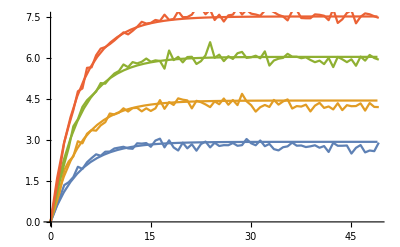

****************************************************

****************************************************

Exporting Template recovery fits with BP+T rate: 0.00491128 0.00001
 P+RQ rate:2.54035×10^-6

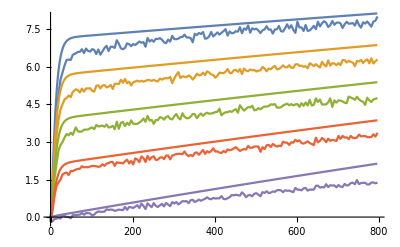

***************************************

***************************************

Exporting Discard Pathway rates

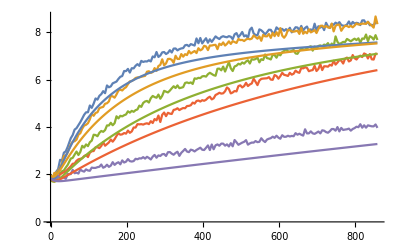

```mathematica
********************************************************************************************************************************************************************************************************************
Exporting the reaction rate constant of reporter characterizaion (BP+RQ<->BPR+Q) and also the concentration of BPR with time as predicted by our simulations
fin=4;(*Select the index of iteration that was best fit*)
con=4;
concV=iter[[fin]];
SetDirectory[ParentDirectory[NotebookDirectory[]]];
var=Import["2. Reporters\\Conc\\"<>str<>"RQi.wl"];
f1[x_]:=var;(*RQ initial concentration*);

concC=Array[f1,4];
Clear[k1,k2];
sol=Array[ff,Length[data]];
For[j=1,j≤Length[data],j++,
q2=data[[1]][[1;;,1]];

sol[[j]]=ParametricNDSolve[{y'[t]==k1*(concC[[j]]-y[t])*(concV[[j]]-y[t])-k2*y[t]^2,y[0]==0},y,{t,q2[[1]],q2[[Length[q2]]]},{k1,k2}]
];
temptable0[x_]:=(
q2=data[[1]][[1;;,1]];
Return[Table[{t,y[rates[[fin]][[1]],rates[[fin]][[2]]][t]/.sol[[x]]},{t,q2[[1]],q2[[Length[q2]]]}]])
emp={};For[j=1,j<=Length[data],j++,
AppendTo[emp,temptable0[j]]]
s1=ListPlot[emp,Joined->True];
s2=ListPlot[data,Joined->True];
(*Export [BPT] vs time as predicted by simulations*)
Export["2. Reporters\\Sim\\"<>str<>".wl",emp];
Print["Exporting Reporter Characterization fits with rate: ", rates[[fin]]];
(*Export the reaction rate constants predicted by simulations*)
Export["BP+RQ rates\\"<>str<>".wl",rates[[fin]]];
(*Export the [BT] that was used to make prediction of reporter characterization*)
Export["2. Reporters\\concBP-"<>str<>".wl",iter[[fin]]];
Show[s1,s2]

Print["****************************************************"]
Print["****************************************************"]

Clear[C1,C2,C3,C4,C5,x,y,z,t,q,k1,k2,k3,k3r,k4];
Po=50;
reverse=1;
concBT=Import["3. Template recovery\\Conc\\BT\\"<>Btype<>Ptype<>".wl"];
C1=concBT;
C3=C1;
C4=concRQred+concPRiTR;
C5=C4;
C2=concPo+concPRiTR;
k3=rates[[fin]][[1]];
k3r=rates[[fin]][[2]];
Clear[k1,k2];
ff[x_]:=0;
(*stores the parametric solution of the different differential equations*)
sol2=Array[ff,Length[datarange]];
For[j=1,j≤Length[datarange],j++,
q=datarange[[j]][[1;;,1]];
 (*c1=c3=[BT]o,c4=c5={rQ]o,c2=[P]o;x=BP, y=RQ,z=PR*)
sol2[[j]]=ParametricNDSolve[{x'[t]==k1*(C1[[j]]-C4[[j]]+z[t]+y[t]-x[t])*(C2[[j]]-C4[[j]]+y[t]-x[t])-k2*x[t]*(C3[[j]]-C1[[j]]+C4[[j]]+x[t]-y[t]-z[t])-k3*x[t]*y[t]+k3r*(C4[[j]]-z[t]-y[t])*(C5[[j]]-y[t]),
y'[t]==-k3*x[t]*y[t]-k4*(C2[[j]]-C4[[j]]+y[t]-x[t])*y[t]+k3r*(C4[[j]]-z[t]-y[t])*(C5[[j]]-y[t]),
z'[t]==k4*(C2[[j]]-C4[[j]]+y[t]-x[t])*y[t],
x[0]==0,y[0]==concRQred[[j]],z[0]==concPRiTR[[j]]},{x,y,z},{t,q[[1]],q[[Length[q]]]},{k1,k2,k4}]
];

temptable[x_]:=(
q=datarange[[1]][[1;;,1]];
Return[Table[{t,concRQred[[x]]+concPRiTR[[x]]-y[RESULT[[fin]][[1]],RESULT[[fin]][[2]],RESULT[[fin]][[3]]][t]/.sol2[[x]]},{t,q[[1]],q[[Length[q]]]}]])


emp={};For[j=1,j<=Length[datarange],j++,
AppendTo[emp,temptable[j]]];
s1=ListPlot[emp,Joined->True];
s2=ListPlot[datarange,Joined->True];
Print["Exporting Template recovery fits with BP+T rate: ", RESULT[[fin]][[1]], " ", RESULT[[fin]][[2]],"\n P+RQ rate:", RESULT[[fin]][[3]]];
Show[s2,s1]
(*export  the conc vs time (for different input reactants)-Template recovery predicted by simulations*)
Export["3. Template recovery\\Sim\\"<>str<>".wl",emp];


(*Export the reaction rate constants of BT+P<->BP+T*)
Export["BT+P rates\\"<>str<>".wl",RESULT[[fin]]];

Print["***************************************"];
Print["***************************************"];

SetDirectory[ParentDirectory[NotebookDirectory[]]];
k1=Import["1. Lock opening and binding\\Rates\\"<>Btype<>"klock.wl"][[1]];
k2=Import["1. Lock opening and binding\\Rates\\"<>Btype<>"klock.wl"][[2]];
Clear[k3,k4,k6];
concT={6,4,2,1,0};
C1=concBL+concBPRiDP;
C2=concPo2+concBPRiDP;
C3=concT;
C4=concRQred2+concBPRiDP;
C5=1.2*(concRQred2+concBPRiDP);
C6=1.2*(concBL+concBPRiDP);
k1=Import["1. Lock opening and binding\\Rates\\"<>Btype<>"klock.wl"][[1]];
k2=Import["1. Lock opening and binding\\Rates\\"<>Btype<>"klock.wl"][[2]];
k5=rates[[fin]][[1]];
k5r=rates[[fin]][[2]];
k7=0;
ff[x_]:=0;

(*stores the parametric solution of the different differential equations*)
sol3=Array[ff,Length[datarangeDP]];
For[j=1,j≤Length[datarangeDP],j++,
q=datarangeDP[[j]][[1;;,1]];
(*
C1=concBL+concBPRiDP;
C2=Po;
C3=concT;
C4=RQo+concBPRiDP[[j]];
C5=RQo;
C6=concBL;
*)
(*a=PR, b=L,x=BT, z=BP,y=RQ;
C1=[BL]o, c2=Po, c3=[T]o, C4=[RQ]o, C5=[RQ]o, C6=[BL]o;
*)
sol3[[j]]=ParametricNDSolve[{x'[t]==k1*(C6[[j]]-b[t])*(C3[[j]]-x[t])-k2*x[t]*b[t]-k3*x[t]*(C2[[j]]-C4[[j]]-z[t]+y[t])+k4*z[t]*(C3[[j]]-x[t]),

z'[t]==k7*(C6[[j]]-b[t])*(C2[[j]]-C4[[j]]-z[t]+y[t])+k3*x[t]*(C2[[j]]-C4[[j]]-z[t]+y[t])-k4*z[t]*(C3[[j]]-x[t])-k5*z[t]*y[t]+k5r*(C4[[j]]-y[t]-a[t])*(C5[[j]]-y[t]),

y'[t]==-k5*z[t]*y[t]-k6*(C2[[j]]-C4[[j]]-z[t]+y[t])*y[t]+k5r*(C4[[j]]-y[t]-a[t])*(C5[[j]]-y[t]),

a'[t]==k6*(C2[[j]]-C4[[j]]-z[t]+y[t])*y[t],

b'[t]==k7*(C6[[j]]-b[t])*(C2[[j]]-C4[[j]]-z[t]+y[t])+k1*(C6[[j]]-b[t])*(C3[[j]]-x[t])-k2*x[t]*b[t],

x[0]==0,y[0]==concRQred2[[j]],z[0]==0,a[0]==0,b[0]==0.2*concBL[[j]]+concBPRiDP[[j]]},{x,y,z,a,b},{t,q[[1]],q[[Length[q]]]},{k3,k4,k6}

]]

temptable2[x_]:=(
q=datarangeDP[[1]][[1;;,1]];
Return[Table[{t,(concRQred2[[x]]+concBPRiDP[[x]]-y[RESULT[[fin]][[1]],RESULT[[fin]][[2]],RESULT[[fin]][[3]]][t]/.sol3[[x]])},{t,q[[1]],q[[Length[q]]]}]])
(*
temptable2[x_]:=(
q=datarangeDP[[1]][[1;;,1]];
Return[Table[RQo-y[0.002,0.0001][t]/.sol3[[x]],{t,q[[1]],q[[Length[q]]]}]])
*)


emp={};For[j=1,j<=Length[datarangeDP],j++,
AppendTo[emp,temptable2[j]]]
s1=ListPlot[emp,Joined->True];
s2=ListPlot[datarangeDP,Joined->True];

Print["Exporting Discard Pathway rates"]
Show[s2,s1]
(*export  the conc vs time (for different input reactants)-Discard pathway predicted by simulations*)

Export["4. Discard Pathway\\Sim\\"<>str<>".wl",emp];
```

********************************************************************************************************************************************************************************************************************
Exporting the reaction rate constant of reporter characterizaion (BP+RQ<->BPR+Q) and also the concentration of BPR with time as predicted by our simulations

Exporting Reporter Characterization fits with rate: {0.00607482,0.0001}

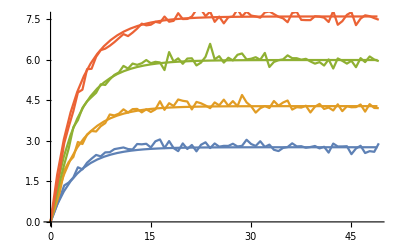

****************************************************

****************************************************

Exporting Template recovery fits with BP+T rate: 0.00207234 0.00512
 P+RQ rate:1.26248×10^-6

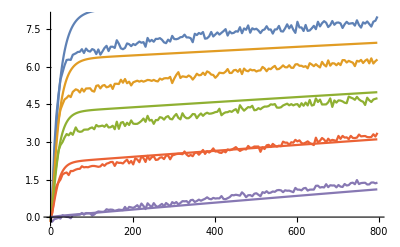

***************************************

***************************************

Exporting Discard Pathway rates

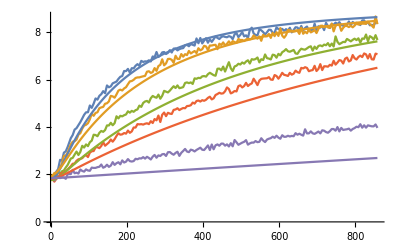

```mathematica
********************************************************************************************************************************************************************************************************************
Exporting the reaction rate constant of reporter characterizaion (BP+RQ<->BPR+Q) and also the concentration of BPR with time as predicted by our simulations
fin=3;(*Select the index of iteration that was best fit*)
con=3;
concV=iter[[fin]];
SetDirectory[ParentDirectory[NotebookDirectory[]]];
var=Import["2. Reporters\\Conc\\"<>str<>"RQi.wl"];
f1[x_]:=var;(*RQ initial concentration*);

concC=Array[f1,4];
Clear[k1,k2];
sol=Array[ff,Length[data]];
For[j=1,j≤Length[data],j++,
q2=data[[1]][[1;;,1]];

sol[[j]]=ParametricNDSolve[{y'[t]==k1*(concC[[j]]-y[t])*(concV[[j]]-y[t])-k2*y[t]^2,y[0]==0},y,{t,q2[[1]],q2[[Length[q2]]]},{k1,k2}]
];
temptable0[x_]:=(
q2=data[[1]][[1;;,1]];
Return[Table[{t,y[rates[[fin]][[1]],rates[[fin]][[2]]][t]/.sol[[x]]},{t,q2[[1]],q2[[Length[q2]]]}]])
emp={};For[j=1,j<=Length[data],j++,
AppendTo[emp,temptable0[j]]]
s1=ListPlot[emp,Joined->True];
s2=ListPlot[data,Joined->True];
(*Export [BPT] vs time as predicted by simulations*)
Export["2. Reporters\\Sim\\"<>str<>"_2.wl",emp];
Print["Exporting Reporter Characterization fits with rate: ", rates[[fin]]];
(*Export the reaction rate constants predicted by simulations*)
Export["BP+RQ rates\\"<>str<>"_2.wl",rates[[fin]]];
(*Export the [BT] that was used to make prediction of reporter characterization*)
Export["2. Reporters\\concBP-"<>str<>"_2.wl",iter[[fin]]];
Show[s1,s2]

Print["****************************************************"]
Print["****************************************************"]

Clear[C1,C2,C3,C4,C5,x,y,z,t,q,k1,k2,k3,k3r,k4];
Po=50;
reverse=1;
concBT=Import["3. Template recovery\\Conc\\BT\\"<>Btype<>Ptype<>".wl"];
C1=concBT;
C3=C1;
C4=concRQred+concPRiTR;
C5=C4;
C2=concPo+concPRiTR;
k3=rates[[fin]][[1]];
k3r=rates[[fin]][[2]];
Clear[k1,k2];
ff[x_]:=0;
(*stores the parametric solution of the different differential equations*)
sol2=Array[ff,Length[datarange]];
For[j=1,j≤Length[datarange],j++,
q=datarange[[j]][[1;;,1]];
 (*c1=c3=[BT]o,c4=c5={rQ]o,c2=[P]o;x=BP, y=RQ,z=PR*)
sol2[[j]]=ParametricNDSolve[{x'[t]==k1*(C1[[j]]-C4[[j]]+z[t]+y[t]-x[t])*(C2[[j]]-C4[[j]]+y[t]-x[t])-k2*x[t]*(C3[[j]]-C1[[j]]+C4[[j]]+x[t]-y[t]-z[t])-k3*x[t]*y[t]+k3r*(C4[[j]]-z[t]-y[t])*(C5[[j]]-y[t]),
y'[t]==-k3*x[t]*y[t]-k4*(C2[[j]]-C4[[j]]+y[t]-x[t])*y[t]+k3r*(C4[[j]]-z[t]-y[t])*(C5[[j]]-y[t]),
z'[t]==k4*(C2[[j]]-C4[[j]]+y[t]-x[t])*y[t],
x[0]==0,y[0]==concRQred[[j]],z[0]==concPRiTR[[j]]},{x,y,z},{t,q[[1]],q[[Length[q]]]},{k1,k2,k4}]
];

temptable[x_]:=(
q=datarange[[1]][[1;;,1]];
Return[Table[{t,concRQred[[x]]+concPRiTR[[x]]-y[RESULT[[fin]][[1]],RESULT[[fin]][[2]],RESULT[[fin]][[3]]][t]/.sol2[[x]]},{t,q[[1]],q[[Length[q]]]}]])


emp={};For[j=1,j<=Length[datarange],j++,
AppendTo[emp,temptable[j]]];
s1=ListPlot[emp,Joined->True];
s2=ListPlot[datarange,Joined->True];
Print["Exporting Template recovery fits with BP+T rate: ", RESULT[[fin]][[1]], " ", RESULT[[fin]][[2]],"\n P+RQ rate:", RESULT[[fin]][[3]]];
Show[s2,s1]
(*export  the conc vs time (for different input reactants)-Template recovery predicted by simulations*)
Export["3. Template recovery\\Sim\\"<>str<>"_2.wl",emp];


(*Export the reaction rate constants of BT+P<->BP+T*)
Export["BT+P rates\\"<>str<>"_2.wl",RESULT[[fin]]];

Print["***************************************"];
Print["***************************************"];

SetDirectory[ParentDirectory[NotebookDirectory[]]];
k1=Import["1. Lock opening and binding\\Rates\\"<>Btype<>"klock.wl"][[1]];
k2=Import["1. Lock opening and binding\\Rates\\"<>Btype<>"klock.wl"][[2]];
Clear[k3,k4,k6];
concT={6,4,2,1,0};
C1=concBL+concBPRiDP;
C2=concPo2+concBPRiDP;
C3=concT;
C4=concRQred2+concBPRiDP;
C5=1.2*(concRQred2+concBPRiDP);
C6=1.2*(concBL+concBPRiDP);
k1=Import["1. Lock opening and binding\\Rates\\"<>Btype<>"klock.wl"][[1]];
k2=Import["1. Lock opening and binding\\Rates\\"<>Btype<>"klock.wl"][[2]];
k5=rates[[fin]][[1]];
k5r=rates[[fin]][[2]];
k7=0;
ff[x_]:=0;

(*stores the parametric solution of the different differential equations*)
sol3=Array[ff,Length[datarangeDP]];
For[j=1,j≤Length[datarangeDP],j++,
q=datarangeDP[[j]][[1;;,1]];
(*
C1=concBL+concBPRiDP;
C2=Po;
C3=concT;
C4=RQo+concBPRiDP[[j]];
C5=RQo;
C6=concBL;
*)
(*a=PR, b=L,x=BT, z=BP,y=RQ;
C1=[BL]o, c2=Po, c3=[T]o, C4=[RQ]o, C5=[RQ]o, C6=[BL]o;
*)
sol3[[j]]=ParametricNDSolve[{x'[t]==k1*(C6[[j]]-b[t])*(C3[[j]]-x[t])-k2*x[t]*b[t]-k3*x[t]*(C2[[j]]-C4[[j]]-z[t]+y[t])+k4*z[t]*(C3[[j]]-x[t]),

z'[t]==k7*(C6[[j]]-b[t])*(C2[[j]]-C4[[j]]-z[t]+y[t])+k3*x[t]*(C2[[j]]-C4[[j]]-z[t]+y[t])-k4*z[t]*(C3[[j]]-x[t])-k5*z[t]*y[t]+k5r*(C4[[j]]-y[t]-a[t])*(C5[[j]]-y[t]),

y'[t]==-k5*z[t]*y[t]-k6*(C2[[j]]-C4[[j]]-z[t]+y[t])*y[t]+k5r*(C4[[j]]-y[t]-a[t])*(C5[[j]]-y[t]),

a'[t]==k6*(C2[[j]]-C4[[j]]-z[t]+y[t])*y[t],

b'[t]==k7*(C6[[j]]-b[t])*(C2[[j]]-C4[[j]]-z[t]+y[t])+k1*(C6[[j]]-b[t])*(C3[[j]]-x[t])-k2*x[t]*b[t],

x[0]==0,y[0]==concRQred2[[j]],z[0]==0,a[0]==0,b[0]==0.2*concBL[[j]]+concBPRiDP[[j]]},{x,y,z,a,b},{t,q[[1]],q[[Length[q]]]},{k3,k4,k6}

]]

temptable2[x_]:=(
q=datarangeDP[[1]][[1;;,1]];
Return[Table[{t,(concRQred2[[x]]+concBPRiDP[[x]]-y[RESULT[[fin]][[1]],RESULT[[fin]][[2]],RESULT[[fin]][[3]]][t]/.sol3[[x]])},{t,q[[1]],q[[Length[q]]]}]])
(*
temptable2[x_]:=(
q=datarangeDP[[1]][[1;;,1]];
Return[Table[RQo-y[0.002,0.0001][t]/.sol3[[x]],{t,q[[1]],q[[Length[q]]]}]])
*)


emp={};For[j=1,j<=Length[datarangeDP],j++,
AppendTo[emp,temptable2[j]]]
s1=ListPlot[emp,Joined->True];
s2=ListPlot[datarangeDP,Joined->True];

Print["Exporting Discard Pathway rates"]
Show[s2,s1]
(*export  the conc vs time (for different input reactants)-Discard pathway predicted by simulations*)

Export["4. Discard Pathway\\Sim\\"<>str<>"_2.wl",emp];
```

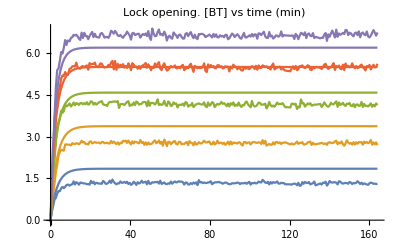

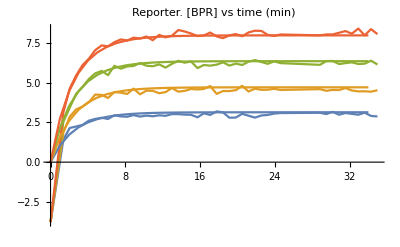

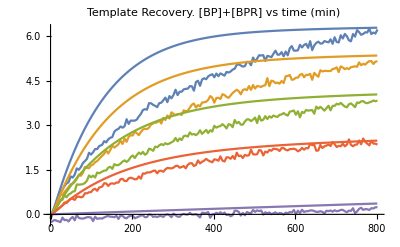

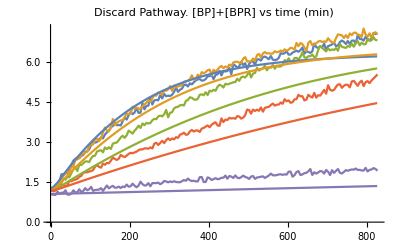

```mathematica
(*EXPORT data as pics and excel format*)
type="B1";
proof="P27-5";
SetDirectory[ParentDirectory[NotebookDirectory[]]];
lockexptdata=Import["1. Lock opening and binding\\Data\\"<>type<>"lockopen.wl"];
lockfitdata=Import["1. Lock opening and binding\\Sim\\Sim_"<>type<>".wl"];

repfitdata=Import["2. Reporters\\Sim\\"<>type<>proof<>".wl"];
repexptdata=Import["2. Reporters\\Data\\"<>type<>proof<>".wl"][[2;;5]];
tempfitdata=Import["3. Template recovery\\Sim\\"<>type<>proof<>".wl"];
tempexptdata=Import["3. Template Recovery\\Data\\"<>type<>proof<>".wl"];
dpfitdata=Import["4. Discard Pathway\\Sim\\"<>type<>proof<>".wl"];
dpexptdata=Import["4. Discard pathway\\Data\\"<>type<>proof<>".wl"];

s1=ListPlot[lockexptdata,Joined->True,PlotLabel->"Lock opening. [BT] vs time (min)"];
s2=ListPlot[lockfitdata,Joined->True];
Show[s1,s2]
Export["Fittings\\Pics\\"<>type<>"_lock_opening_pic.png",Show[s1,s2]];

s1=ListPlot[repexptdata,Joined->True,PlotLabel->"Reporter. [BPR] vs time (min)"];
s2=ListPlot[repfitdata,Joined->True];
Show[s1,s2]
Export["Fittings\\Pics\\"<>type<>proof<>"_reporter_pic.png",Show[s1,s2]];

s1=ListPlot[tempexptdata,Joined->True,PlotLabel->"Template Recovery. [BP]+[BPR] vs time (min)"];
s2=ListPlot[tempfitdata,Joined->True];
Show[s1,s2]
Export["Fittings\\Pics\\"<>type<>proof<>"_template_recovery_pic.png",Show[s1,s2]];


s1=ListPlot[dpexptdata,Joined->True,PlotLabel->"Discard Pathway. [BP]+[BPR] vs time (min)"];
s2=ListPlot[dpfitdata,Joined->True];
Show[s1,s2]
Export["Fittings\\Pics\\"<>type<>proof<>"_discard_pathway_pic.png",Show[s1,s2]];


data={lockexptdata[[1]][[1;;,1]]};
data2={lockfitdata[[1]][[1;;,1]]};
For[i=1,i<=Length[lockexptdata],i++,
AppendTo[data,lockexptdata[[i]][[1;;,2]]];
AppendTo[data2,lockfitdata[[i]][[1;;,2]]]];
Export["Fittings\\"<>proof<>"\\"<>type<>"_Lock_opening.xlsx",{"Experiments"->Transpose[data],"Simulations"->Transpose[data2]}];

data={repexptdata[[1]][[1;;,1]]};
data2={repfitdata[[1]][[1;;,1]]};
For[i=1,i<=Length[repexptdata],i++,
AppendTo[data,repexptdata[[i]][[1;;,2]]];
AppendTo[data2,repfitdata[[i]][[1;;,2]]]];
Export["Fittings\\"<>proof<>"\\"<>type<>proof<>"_reporter.xlsx",{"Experiments"->Transpose[data],"Simulations"->Transpose[data2]}];

data={tempexptdata[[1]][[1;;,1]]};
data2={tempfitdata[[1]][[1;;,1]]};
For[i=1,i<=Length[tempexptdata],i++,
AppendTo[data,tempexptdata[[i]][[1;;,2]]];
AppendTo[data2,tempfitdata[[i]][[1;;,2]]]];
Export["Fittings\\"<>proof<>"\\"<>type<>proof<>"_template_recovery.xlsx",{"Experiments"->Transpose[data],"Simulations"->Transpose[data2]}];

data={dpexptdata[[1]][[1;;,1]]};
data2={dpfitdata[[1]][[1;;,1]]};
For[i=1,i<=Length[dpexptdata],i++,
AppendTo[data,dpexptdata[[i]][[1;;,2]]];
AppendTo[data2,dpfitdata[[i]][[1;;,2]]]];
Export["Fittings\\"<>proof<>"\\"<>type<>proof<>"_discard_pathway.xlsx",{"Experiments"->Transpose[data],"Simulations"->Transpose[data2]}];
```

```mathematica
The calculation of BT+P and P+RQ rates can also be done with this code below. It also generates intermediary figures.
```

```mathematica
diff=1;
lim=5;(*Num of conc to consider*)
RESULT={};
fig1={};
fig2={};
(*Start the iteartion for different starting configurations of [BP] and therefore the different reaction rate constants derived for BP+RQ<->BPR+Q*)
For[con=1,con<=Length[iter],con++,
Print["Iteration: ",con];
t1=AbsoluteTime[];
(*Pipeline to calculate MSD is similar to the pipeline defined in Lock_opening_final.nb *)
tabdiff[y_,t_,k1_,k2_,k3_,j_]:=(q=t[[1;;,1]];
p=Table[{q[[i]],concRQred[[j]]+concPRiTR[[j]]-y[k1,k2,k3][q[[i]]]/.sol2[[j]][[2]]},{i,1,Length[q],diff}];
p0=Table[{q[[i]],t[[i]][[2]]},{i,1,Length[q],diff}];
p1=Table[p[[i]][[2]]-p0[[i]][[2]],{i,1,Length[p],1}];
Return[{p0,p1}];);

Clear[C1,C2,C3,C4,C5,x,y,z,t,q,k1,k2,k3,k3r,k4];
Po=50;
reverse=1;
concBT=Import["3. Template recovery\\Conc\\BT\\"<>Btype<>Ptype<>".wl"];
C1=concBT;
C3=C1;
C4=concRQred+concPRiTR;
C5=C4;
C2=concPo+concPRiTR;
k3=rates[[con]][[1]];
k3r=rates[[con]][[2]];
k4=prqrate;
q=datarange[[1]][[1;;,1]];
Clear[k4];
ff[x_]:=0;
(*stores the parametric solution of the different differential equations*)
sol2=Array[ff,Length[datarange]];
For[j=1,j≤Length[datarange],j++,
 (*c1=c3=[BT]o,c4=c5={rQ]o,c2=[P]o;x=BP, y=RQ,z=PR*)
sol2[[j]]=ParametricNDSolve[{x'[t]==k1*(C1[[j]]-C4[[j]]+z[t]+y[t]-x[t])*(C2[[j]]-C4[[j]]+y[t]-x[t])-k2*x[t]*(C3[[j]]-C1[[j]]+C4[[j]]+x[t]-y[t]-z[t])-k3*x[t]*y[t]+k3r*(C4[[j]]-z[t]-y[t])*(C5[[j]]-y[t]),
y'[t]==-k3*x[t]*y[t]-k4*(C2[[j]]-C4[[j]]+y[t]-x[t])*y[t]+k3r*(C4[[j]]-z[t]-y[t])*(C5[[j]]-y[t]),
z'[t]==k4*(C2[[j]]-C4[[j]]+y[t]-x[t])*y[t],
x[0]==0,y[0]==concRQred[[j]],z[0]==concPRiTR[[j]]},{x,y,z},{t,q[[1]],q[[Length[q]]]},{k1,k2,k4}]];

tabdiff2[y_,t_,k1_,k2_,k3_,j_]:=(
q=t[[1;;,1]];
p=Table[{q[[i]],concRQred2[[j]]+concBPRiDP[[j]]-y[k1,k2,k3][q[[i]]]/.sol3[[j]][[2]]},{i,1,Length[q],diff}];
p0=Table[{q[[i]],t[[i]][[2]]},{i,1,Length[q],diff}];
p1=Table[p[[i]][[2]]-p0[[i]][[2]],{i,1,Length[p],1}];
Return[{p0,p1}];);


Clear[C1,C2,C3,C4,C5,k1,k2,k3,k3r,k4,k5,k5r,k6];
concT={6,4,2,1,0};
C1=concBL+concBPRiDP;
C2=concPo2+concBPRiDP;
C3=concT;
C4=concRQred2+concBPRiDP;
C5=concRQred2;
C6=C1;
k1=Import["1. Lock opening and binding\\Rates\\"<>Btype<>"klock.wl"][[1]];
k2=Import["1. Lock opening and binding\\Rates\\"<>Btype<>"klock.wl"][[2]];
k5=rates[[con]][[1]];
k5r=rates[[con]][[2]];
k6=prqrate;
Clear[k6];
k7=0;
ff[x_]:=0;
(*stores the parametric solution of the different differential equations*)
sol3=Array[ff,Length[datarangeDP]];
For[j=1,j≤Length[datarangeDP],j++,
q=datarangeDP[[j]][[1;;,1]];
(*
C1=concBL+concBPRiDP;
C2=Po;
C3=concT;
C4=RQo+concBPRiDP[[j]];
C5=RQo;
C6=concBL;
*)
(*a=PR, b=L,x=BT, z=BP,y=RQ;
C1=[BL]o, c2=Po, c3=[T]o, C4=[RQ]o, C5=[RQ]o, C6=[BL]o;
*)
sol3[[j]]=ParametricNDSolve[{x'[t]==k1*(C6[[j]]-b[t])*(C3[[j]]-x[t])-k2*x[t]*b[t]-k3*x[t]*(C2[[j]]-C4[[j]]-z[t]+y[t])+k4*z[t]*(C3[[j]]-x[t]),

z'[t]==k7*(C6[[j]]-b[t])*(C2[[j]]-C4[[j]]-z[t]+y[t])+k3*x[t]*(C2[[j]]-C4[[j]]-z[t]+y[t])-k4*z[t]*(C3[[j]]-x[t])-k5*z[t]*y[t]+k5r*(C4[[j]]-y[t]-a[t])*(C5[[j]]-y[t]),

y'[t]==-k5*z[t]*y[t]-k6*(C2[[j]]-C4[[j]]-z[t]+y[t])*y[t]+k5r*(C4[[j]]-y[t]-a[t])*(C5[[j]]-y[t]),

a'[t]==k6*(C2[[j]]-C4[[j]]-z[t]+y[t])*y[t],

b'[t]==k7*(C6[[j]]-b[t])*(C2[[j]]-C4[[j]]-z[t]+y[t])+k1*(C6[[j]]-b[t])*(C3[[j]]-x[t])-k2*x[t]*b[t],

x[0]==0,y[0]==concRQred2[[j]],z[0]==0,a[0]==0,b[0]==0},{x,y,z,a,b},{t,q[[1]],q[[Length[q]]]},{k3,k4,k6}

]];


(*Technique#3: Parameter fit that minimizes overall tries to fit for initial times*)
(*Start numerical evaluation of the parameter space*)
Tinterest=800;
kstart=0.0004;
kend=0.001;
kstart2=0.0001;
kend2=0.0005;
kstart3=0.8*10^-6;
kend3=2*10^-6;
fact=1.5;(*How often to increase k1*)
fact2=1.5;(*How often to increase k2*)
fact3=1.5;(*How often to increase k3*)
reverse=1;
reverse2=1;
(*kstart2=0.001;*)
If[reverse==0,kstart2=1;kend2=1];
No=IntegerPart[Log[(kend/kstart)]/Log[fact]]+1;
No2=IntegerPart[Log[(kend*400/kstart)]/Log[fact2]]+2;
No3=IntegerPart[Log[(kend3/kstart3)]/Log[fact3]]+2;
Print["Num iteration:", No*No2*No3,"?"];
If[reverse2==0,No2=1];
f0[x_,y_,z_]:=0;
error=Array[f0,{No,No2,No3}];
error2={};
c1=1;
result=1000000;
result3={kstart,kstart2,kstart3};
t3=AbsoluteTime[];
For[k10=kstart,k10≤kend,k10=k10*fact,
c10=1;
For[k20=k10/20,k20≤20*k10,k20=k20*fact2,
c100=1;
For[k30=kstart3,k30<=kend3,k30=k30*fact3,
temp0=0;
For[j=1,j≤Length[datarange[[1;;lim]]],j++,
hello=tabdiff[y,datarange[[j]],k10,k20,k30,j];
temparr=hello[[2]];
ttt=hello[[1]];
For[i=1,i<=Length[temparr],i++,
sump=0;
If[ttt[[i]][[1]]<Tinterest,
sump+=1.0(temparr[[i]]*temparr[[i]]),
sump+=0.2(temparr[[i]]*temparr[[i]])
];
temp0+=sump;
];
hello=tabdiff2[y,datarangeDP[[j]],k10,k20,k30,j];
temparr2=hello[[2]];
ttt=hello[[1]];
For[i=1,i<=Length[temparr2],i++,
sump=0;
If[ttt[[i]][[1]]<Tinterest,
sump+=1.0(temparr2[[i]]*temparr2[[i]]),
sump+=0.2(temparr2[[i]]*temparr2[[i]])
];
temp0+=sump;
]
];
temp=temp0;
If[c1==1 &&c10==1&&c100==1, result=temp];
error[[c1]][[c10]][[c100++]]=temp;
error2=AppendTo[error2,{Log[k10],Log[k20],Log[k30],temp}];
(*If new difference between lists is small, remember that parameter set*)
If[temp-result<-0.01,result=temp;result3={k10,k20,k30,temp}];
]c10++;
]c1++;
];
Print["Reaction fit for BT+P<->BP+T: ",result3[[1]],", ",result3[[2]]];
Print["Reaction fit for P+RQ->PR+Q: ",result3[[3]]];
Print["Error: ",result3[[4]]];
t4=AbsoluteTime[];
AppendTo[RESULT,result3];

finplot[k_]:=(
SeedRandom[k+1];
xx=RandomReal[];
yy=RandomReal[];
zz=RandomReal[];
For[j=1,j≤Length[datarange],j++,
q=datarange[[j]][[1;;,1]];
s1=ListPlot[datarange[[k]],Joined->True,PlotRange->All,PlotStyle->RGBColor[xx,yy,zz]];
s2=Plot[If[reverse==1,concRQred[[j]]+concPRiTR[[j]]-y[result3[[1]],result3[[2]],result3[[3]]][t]/.sol2[[k]],RQo-y[result3[[1]]][t]/.sol2[[k]]],{t,q[[1]],q[[Length[q]]]},PlotRange->{0,10},PlotStyle->RGBColor[xx,yy,zz],PlotLegends->{ToString[Round[concBT[[k]],.1]]<>"nM BT"}];
s2=Show[s2,s1];
Return[s2]]);

Print["Template Recovery fit:"];
Print[Show[{finplot[5],finplot[4],finplot[3],finplot[2],finplot[1]}]];
Print["***************************************************"];
AppendTo[fig1,Show[{finplot[5],finplot[4],finplot[3],finplot[2],finplot[1]}]];

finplot[k_]:=(
SeedRandom[k+3];
xx=RandomReal[];
yy=RandomReal[];
zz=RandomReal[];
For[j=1,j≤Length[datarangeDP],j++,
s1=ListPlot[datarangeDP[[k]],Joined->True,PlotRange->All,PlotStyle->RGBColor[xx,yy,zz]];
s2=Plot[concRQred2[[j]]+concBPRiDP[[j]]-y[result3[[1]],result3[[2]],result3[[3]]][t]/.sol3[[k]],{t,q[[1]],q[[Length[q]]]},PlotRange->{0,10},PlotStyle->RGBColor[xx,yy,zz],PlotLegends->{ToString[concT[[k]]]<>"nM T"}];
s2=Show[s2,s1];Return[s2]]);

Print["Discard pathway fit:"];
Print[Show[{finplot[5],finplot[4],finplot[3],finplot[2],finplot[1]}]];
Print["***************************************************"];
Print["***************************************************"];
AppendTo[fig2,Show[{finplot[5],finplot[4],finplot[3],finplot[2],finplot[1]}]];
Print[Show[{finplot[5],finplot[4],finplot[3],finplot[2],finplot[1]}]];
t2=AbsoluteTime[]
(*Print[t2-t1];*)
]//AbsoluteTiming
s2=ListPlot[datarangeDP,Joined->True,PlotRange->All];
q=datarangeDP[[1]][[1;;,1]];
```